```mathematica
Plot3D[0.5-Cos[q1]Sin[q2]/.{q1->Q1*3.14/180,q2->Q2*3.14/180},{Q1,-180,180},{Q2,-90,90}]
```

-Graphics3D-

```mathematica
Plot3D[0.5-Sin[q1]Sin[q2]/.{q1->Q1*3.14/180,q2->Q2*3.14/180},{Q1,-180,180},{Q2,-90,90}]
```

-Graphics3D-

```mathematica
Show[Plot3D[100*((-0.1+Sin[q1]Sin[q2])^2+(-0.1+Cos[q1]Sin[q2])^2)/.{q1->Q1*3.14/180,q2->Q2*3.14/360},{Q1,-180,180},{Q2,-180,180},PerformanceGoal->"Quality",ColorFunction-> Hue,TicksStyle->Directive[10,Bold],BoundaryStyle->Thick],Graphics3D[Sphere[{45,8,10},10]]]
```

-Graphics3D-

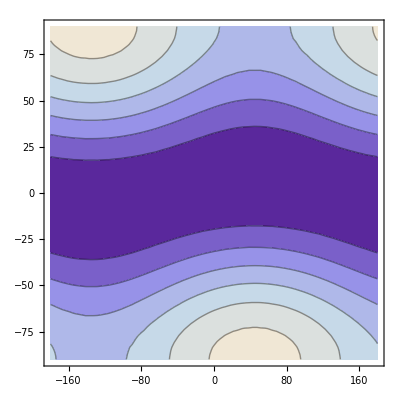

```mathematica
ContourPlot[(-0.1+Sin[q1]Sin[q2])^2+(-0.1+Cos[q1]Sin[q2])^2/.{q1->Q1*3.14/180,q2->Q2*3.14/180},{Q1,-180,180},{Q2,-90,90},PerformanceGoal->"Quality",WorkingPrecision->200]
```

```mathematica
ArcTan[0.1/0.1]/Degree
ArcSin[(1 √(0.1^2+0.1^2))/1]/Degree
```

45.

8.1301

```mathematica
(-0.1+Sin[q1]Sin[q2])^2+(-0.1+Cos[q1]Sin[q2])^2/.{q1->45*3.14/180,q2->8.13010235415598*3.14/180}
```

8.2404×10^-9

```mathematica
-0.1+Cos[q1]Sin[q2]/.{q1->45*3.14/180,q2->8.13010235415598*3.14/180}
```

-0.0000105669

```mathematica
-0.1+Sin[q1]Sin[q2]/.{q1->45*3.14/180,q2->8.13010235415598*3.14/180}
```

-0.0000901595

```mathematica
ParametricPlot[{Sin[q1]Sin[q2]/.{q1->Q1*3.15/180,q2->Q2*3.15/180},Cos[q1]Sin[q2]/.{q1->Q1*3.15/180,q2->Q2*3.15/180}},{Q1,-180,180},{Q2,-90,90}]
```